```mathematica
2+2
```

4

```mathematica
1000!
```

402387260077093773543702433923003985719374864210714632543799910429938512398629020592044208486969404800479988610197196058631666872994808558901323829669944590997424504087073759918823627727188732519779505950995276120874975462497043601418278094646496291056393887437886487337119181045825783647849977012476632889835955735432513185323958463075557409114262417474349347553428646576611667797396668820291207379143853719588249808126867838374559731746136085379534524221586593201928090878297308431392844403281231558611036976801357304216168747609675871348312025478589320767169132448426236131412508780208000261683151027341827977704784635868170164365024153691398281264810213092761244896359928705114964975419909342221566832572080821333186116811553615836546984046708975602900950537616475847728421889679646244945160765353408198901385442487984959953319101723355556602139450399736280750137837615307127761926849034352625200015888535147331611702103968175921510907788019393178114194545257223865541461062892187960223838971476088506276862967146674697562911234082439208160153780889893964518263243671616762179168909779911903754031274622289988005195444414282012187361745992642956581746628302955570299024324153181617210465832036786906117260158783520751516284225540265170483304226143974286933061690897968482590125458327168226458066526769958652682272807075781391858178889652208164348344825993266043367660176999612831860788386150279465955131156552036093988180612138558600301435694527224206344631797460594682573103790084024432438465657245014402821885252470935190620929023136493273497565513958720559654228749774011413346962715422845862377387538230483865688976461927383814900140767310446640259899490222221765904339901886018566526485061799702356193897017860040811889729918311021171229845901641921068884387121855646124960798722908519296819372388642614839657382291123125024186649353143970137428531926649875337218940694281434118520158014123344828015051399694290153483077644569099073152433278288269864602789864321139083506217095002597389863554277196742822248757586765752344220207573630569498825087968928162753848863396909959826280956121450994871701244516461260379029309120889086942028510640182154399457156805941872748998094254742173582401063677404595741785160829230135358081840096996372524230560855903700624271243416909004153690105933983835777939410970027753472000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
N[Pi,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

```mathematica
Manipulate[Plot[Sin[a x],{x,0,10}],{a,1,5}]
```

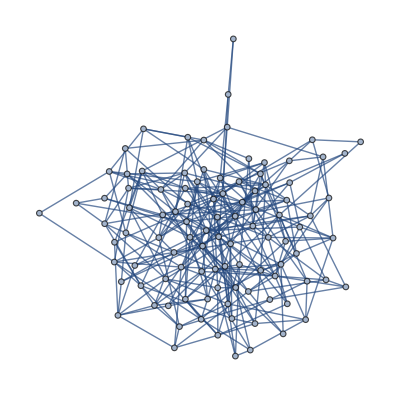

```mathematica
RandomGraph[{100,300}]
```

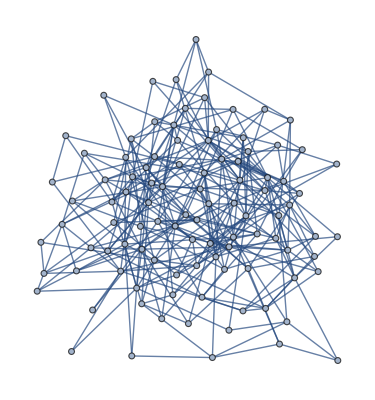
```mathematica
CommunityGraphPlot[-Graphics-]
```

-Graphics-

```mathematica
CurrentImage[]
```

-Graphics-

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
ChromaticityPlot3D[-Graphics-]
```

-Graphics3D-

```mathematica
LinguisticAssistant["Population"]
```

8550405 people

```mathematica
Table[GeoGraphics[GeoDisk[LinguisticAssistant,Quantity[10^n,"Mile"] ]],{n,0,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Rasterize/@Alphabet[]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FeatureSpacePlot[%]
```

-Graphics-

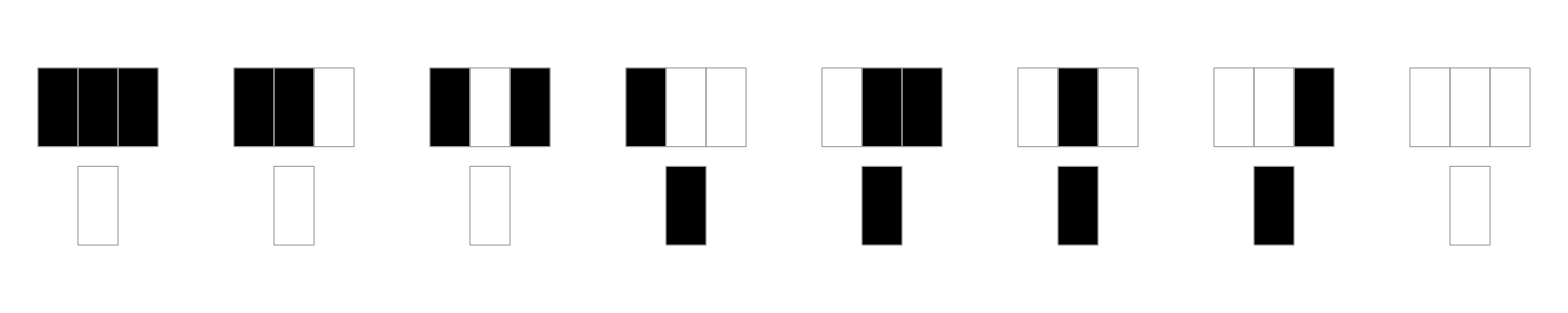

```mathematica
RulePlot[CellularAutomaton[30]]
```

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},400]]
```

-Graphics-

```mathematica
Table[ArrayPlot[CellularAutomaton[n,{{1},0},{50,All}]],{n,0,63}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CenterArray[{1},20,0]
```

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
NestList[RotateLeft[#]+RotateRight[#]&,CenterArray[{1},20,0],10]/. 0->""//Grid
```

|  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 1 |  | 1 |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 1 |  | 2 |  | 1 |  |  |  |  |  |  |  | 
 |  |  |  |  |  | 1 |  | 3 |  | 3 |  | 1 |  |  |  |  |  |  | 
 |  |  |  |  | 1 |  | 4 |  | 6 |  | 4 |  | 1 |  |  |  |  |  | 
 |  |  |  | 1 |  | 5 |  | 10 |  | 10 |  | 5 |  | 1 |  |  |  |  | 
 |  |  | 1 |  | 6 |  | 15 |  | 20 |  | 15 |  | 6 |  | 1 |  |  |  | 
 |  | 1 |  | 7 |  | 21 |  | 35 |  | 35 |  | 21 |  | 7 |  | 1 |  |  | 
 | 1 |  | 8 |  | 28 |  | 56 |  | 70 |  | 56 |  | 28 |  | 8 |  | 1 |  | 
1 |  | 9 |  | 36 |  | 84 |  | 126 |  | 126 |  | 84 |  | 36 |  | 9 |  | 1 | 
 | 10 |  | 45 |  | 120 |  | 210 |  | 252 |  | 210 |  | 120 |  | 45 |  | 10 |  | 2

```mathematica
NestList[RotateLeft[#]+RotateRight[#]&,CenterArray[{1},40,0],20]/. 0->""//Grid
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 2 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 3 |  | 3 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 4 |  | 6 |  | 4 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 5 |  | 10 |  | 10 |  | 5 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 6 |  | 15 |  | 20 |  | 15 |  | 6 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 7 |  | 21 |  | 35 |  | 35 |  | 21 |  | 7 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  | 1 |  | 8 |  | 28 |  | 56 |  | 70 |  | 56 |  | 28 |  | 8 |  | 1 |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  | 1 |  | 9 |  | 36 |  | 84 |  | 126 |  | 126 |  | 84 |  | 36 |  | 9 |  | 1 |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  | 1 |  | 10 |  | 45 |  | 120 |  | 210 |  | 252 |  | 210 |  | 120 |  | 45 |  | 10 |  | 1 |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 1 |  | 11 |  | 55 |  | 165 |  | 330 |  | 462 |  | 462 |  | 330 |  | 165 |  | 55 |  | 11 |  | 1 |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 1 |  | 12 |  | 66 |  | 220 |  | 495 |  | 792 |  | 924 |  | 792 |  | 495 |  | 220 |  | 66 |  | 12 |  | 1 |  |  |  |  |  |  |  | 
 |  |  |  |  |  | 1 |  | 13 |  | 78 |  | 286 |  | 715 |  | 1287 |  | 1716 |  | 1716 |  | 1287 |  | 715 |  | 286 |  | 78 |  | 13 |  | 1 |  |  |  |  |  |  | 
 |  |  |  |  | 1 |  | 14 |  | 91 |  | 364 |  | 1001 |  | 2002 |  | 3003 |  | 3432 |  | 3003 |  | 2002 |  | 1001 |  | 364 |  | 91 |  | 14 |  | 1 |  |  |  |  |  | 
 |  |  |  | 1 |  | 15 |  | 105 |  | 455 |  | 1365 |  | 3003 |  | 5005 |  | 6435 |  | 6435 |  | 5005 |  | 3003 |  | 1365 |  | 455 |  | 105 |  | 15 |  | 1 |  |  |  |  | 
 |  |  | 1 |  | 16 |  | 120 |  | 560 |  | 1820 |  | 4368 |  | 8008 |  | 11440 |  | 12870 |  | 11440 |  | 8008 |  | 4368 |  | 1820 |  | 560 |  | 120 |  | 16 |  | 1 |  |  |  | 
 |  | 1 |  | 17 |  | 136 |  | 680 |  | 2380 |  | 6188 |  | 12376 |  | 19448 |  | 24310 |  | 24310 |  | 19448 |  | 12376 |  | 6188 |  | 2380 |  | 680 |  | 136 |  | 17 |  | 1 |  |  | 
 | 1 |  | 18 |  | 153 |  | 816 |  | 3060 |  | 8568 |  | 18564 |  | 31824 |  | 43758 |  | 48620 |  | 43758 |  | 31824 |  | 18564 |  | 8568 |  | 3060 |  | 816 |  | 153 |  | 18 |  | 1 |  | 
1 |  | 19 |  | 171 |  | 969 |  | 3876 |  | 11628 |  | 27132 |  | 50388 |  | 75582 |  | 92378 |  | 92378 |  | 75582 |  | 50388 |  | 27132 |  | 11628 |  | 3876 |  | 969 |  | 171 |  | 19 |  | 1 | 
 | 20 |  | 190 |  | 1140 |  | 4845 |  | 15504 |  | 38760 |  | 77520 |  | 125970 |  | 167960 |  | 184756 |  | 167960 |  | 125970 |  | 77520 |  | 38760 |  | 15504 |  | 4845 |  | 1140 |  | 190 |  | 20 |  | 2

```mathematica
Table[Mod[n,2],{n,10}]
```

{1,0,1,0,1,0,1,0,1,0}

```mathematica
NestList[Mod[RotateLeft[#]+RotateRight[#],2]&,CenterArray[{1},20,0],10]/. 0->""//Grid
```

|  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 1 |  | 1 |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 1 |  |  |  | 1 |  |  |  |  |  |  |  | 
 |  |  |  |  |  | 1 |  | 1 |  | 1 |  | 1 |  |  |  |  |  |  | 
 |  |  |  |  | 1 |  |  |  |  |  |  |  | 1 |  |  |  |  |  | 
 |  |  |  | 1 |  | 1 |  |  |  |  |  | 1 |  | 1 |  |  |  |  | 
 |  |  | 1 |  |  |  | 1 |  |  |  | 1 |  |  |  | 1 |  |  |  | 
 |  | 1 |  | 1 |  | 1 |  | 1 |  | 1 |  | 1 |  | 1 |  | 1 |  |  | 
 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 
1 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  | 1 |  | 1 | 
 |  |  | 1 |  |  |  |  |  |  |  |  |  |  |  | 1 |  |  |  |

```mathematica
ArrayPlot[NestList[Mod[RotateLeft[#]+RotateRight[#],2]&,CenterArray[{1},50,0],30]]
```

-Graphics-

```mathematica
ArrayPlot[NestList[Mod[RotateLeft[#]+RotateRight[#],5]&,CenterArray[{1},100,0],50]]
```

-Graphics-

```mathematica
ArrayPlot[NestList[Mod[(1+RotateLeft[#])*(2+RotateRight[#]),5]&,CenterArray[{1},100,0],50]]
```

-Graphics-

```mathematica
ArrayPlot[NestList[Mod[(1+RotateLeft[#])*(2+RotateRight[#]),3]&,CenterArray[{1},100,0],50]]
```

-Graphics-

```mathematica
Table[ArrayPlot[NestList[Mod[(a+RotateLeft[#])*(b+RotateRight[#]),2]&,CenterArray[{1},100,0],50]],{a,0,1},{b,0,1}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[ArrayPlot[NestList[Mod[(a+RotateLeft[#])*(b+RotateRight[#]),3]&,CenterArray[{1},100,0],50]],{a,0,2},{b,0,2}]
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot[NestList[RotateRight[Mod[(1+RotateLeft[#])*(2+RotateRight[#]),3]]&,CenterArray[{1},100,0],50]]
```

-Graphics-

```mathematica
ArrayPlot[Take[NestList[RotateRight[Mod[(1+RotateLeft[#])*(2+RotateRight[#]),3]]&,CenterArray[{1},200,0],200],1;;-1;;2]]
```

-Graphics-

```mathematica
ArrayPlot[Take[NestList[RotateRight[Mod[(1+RotateLeft[#])*(2+RotateRight[#]),3]]&,CenterArray[{1},3000,0],3000],1;;-1;;2]]
```

-Graphics-

```mathematica
ArrayPlot[Take[NestList[RotateRight[Mod[(1+RotateLeft[#])*(2+RotateRight[#]),3]]&,CenterArray[{1},3000,0],3000],1;;-1;;2],ColorRules->{0->Black,1->Red,2->Blue}]
```

-Graphics-

```mathematica
(First[#]-#)&[Flatten[FirstPosition[Reverse[#],1|2]&/@Take[NestList[RotateRight[Mod[(1+RotateLeft[#])*(2+RotateRight[#]),3]]&,CenterArray[{1},2000,0],2000],1;;-1;;2]]]
```

{0,0,2,4,6,6,8,8,10,10,10,12,14,14,14,14,16,16,18,20,22,22,22,22,22,22,24,24,26,26,26,26,26,26,26,28,30,30,30,30,30,30,30,30,32,32,34,36,38,38,40,40,42,42,42,42,42,42,42,42,42,42,42,44,46,46,46,46,48,48,50,52,54,54,56,56,58,58,58,60,62,62,62,62,62,62,62,62,64,64,66,68,70,70,70,70,70,70,72,72,74,74,74,76,78,78,78,78,78,78,78,78,80,80,82,84,86,86,88,88,90,90,90,92,94,94,94,94,94,94,94,94,94,94,94,94,96,96,98,100,102,102,104,104,106,106,106,108,110,110,110,110,110,110,110,110,112,112,114,116,118,118,120,120,122,122,122,124,126,126,126,126,128,128,130,132,134,134,136,136,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,140,142,142,142,142,142,142,142,142,144,144,146,148,150,150,152,152,154,154,154,156,158,158,158,158,158,158,158,158,160,160,162,164,166,166,168,168,170,170,170,172,174,174,174,174,174,174,174,174,176,176,178,180,182,182,182,182,182,182,182,182,182,182,184,184,186,186,186,188,190,190,190,190,190,190,190,190,192,192,194,196,198,198,200,200,202,202,202,204,206,206,206,206,206,206,206,206,208,208,210,212,214,214,216,216,218,218,218,220,222,222,222,222,222,222,222,222,224,224,226,228,230,230,232,232,234,234,234,236,238,238,238,238,240,240,242,244,246,246,246,246,246,246,246,246,246,246,248,248,250,250,250,252,254,254,254,254,256,256,258,260,262,262,264,264,266,266,266,266,266,266,266,266,266,266,266,266,266,266,266,268,270,270,270,270,270,270,270,270,272,272,274,276,278,278,278,278,278,278,278,278,278,278,278,278,278,278,280,280,282,282,282,282,282,282,282,284,286,286,286,286,288,288,290,292,294,294,296,296,298,298,298,300,302,302,302,302,304,304,306,308,310,310,312,312,314,314,314,316,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,318,320,320,322,324,326,326,328,328,330,330,330,330,330,330,330,330,330,330,330,332,334,334,334,334,334,334,334,334,334,334,334,334,336,336,338,340,342,342,344,344,346,346,346,348,350,350,350,350,352,352,354,356,358,358,360,360,362,362,362,362,362,362,362,364,366,366,366,366,368,368,370,372,374,374,374,374,374,374,374,374,374,374,376,376,378,378,378,380,382,382,382,382,384,384,386,388,390,390,390,390,390,390,392,392,394,394,394,396,398,398,398,398,398,398,398,398,398,398,398,398,398,398,398,398,400,400,402,404,406,406,408,408,410,410,410,412,414,414,414,414,416,416,418,420,422,422,424,424,426,426,426,428,430,430,430,430,430,430,430,430,430,430,430,430,432,432,434,436,438,438,440,440,442,442,442,442,442,442,442,444,446,446,446,446,448,448,450,452,454,454,454,454,454,454,456,456,458,458,458,460,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,462,464,464,466,468,470,470,472,472,474,474,474,474,474,474,474,474,474,474,474,474,474,474,474,476,478,478,478,478,478,478,478,478,478,478,478,478,478,478,478,478,478,478,478,478,480,480,482,484,486,486,486,486,486,486,488,488,490,490,490,492,494,494,494,494,494,494,494,494,494,494,494,494,496,496,498,500,502,502,504,504,506,506,506,508,510,510,510,510,510,510,510,510,510,510,510,510,510,510,510,510,510,510,510,510,512,512,514,516,518,518,520,520,522,522,522,522,522,522,522,522,522,522,522,524,526,526,526,526,528,528,530,532,534,534,536,536,538,538,538,540,542,542,542,542,542,542,542,542,542,542,542,542,542,542,542,542,544,544,546,548,550,550,552,552,554,554,554,556,558,558,558,558,558,558,558,558,560,560,562,564,566,566,566,566,566,566,568,568,570,570,570,572,574,574,574,574,576,576,578,580,582,582,584,584,586,586,586,588,590,590,590,590,590,590,590,590,592,592,594,596,598,598,598,598,598,598,598,598,598,598,598,598,598,598,598,598,598,598,598,598,598,598,600,600,602,602,602,602,602,602,602,604,606,606,606,606,608,608,610,612,614,614,616,616,618,618,618,620,622,622,622,622,624,624,626,628,630,630,630,630,630,630,630,630,630,630,630,630,630,630,632,632,634,634,634,636,638,638,638,638,638}

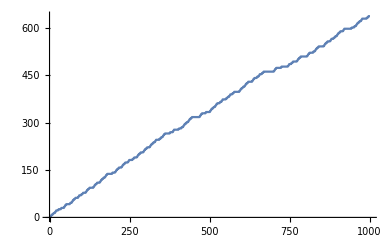

```mathematica
ListLinePlot[%]
```

```mathematica
Fit[%32,{1,x},x]
```

20.7895+0.627946 x

```mathematica
Differences[%32]
```

{0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,0,0,0,0,2,0,2,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,0,0,0,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,0,0,0,0,0,0,0,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,0,0,0,0,0,0,0,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,0,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,0,0,0,0,2,2,0,0,0,2,0,2,2,2,0,0,0,0,0,0,0,0,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,0,0,0,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,0,0,0,0,2,2,0,0,0,2,0,2,2,2,0,0,0,0,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,0,0,0,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,0,0,0,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,0,0,0,0,2,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,0,0,0,2,2,0,0,0,2,0,2,2,2,0,2,0,2,0,0,2,2,0,0,0,2,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,2,2,0,0,0,0}

```mathematica
Split[%]
```

{{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0,0,0,0,0},{2},{0},{2},{0,0,0,0,0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0,0,0,0,0,0,0,0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0,0,0,0,0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0,0,0,0,0,0,0,0,0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0,0,0,0,0,0,0,0,0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2},{0,0,0,0,0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0,0,0,0,0,0,0,0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0,0,0,0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0,0,0,0,0,0,0,0,0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0,0,0,0,0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0,0,0,0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0,0,0,0,0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0,0,0,0,0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0,0,0,0,0,0,0,0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0,0,0,0,0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0,0,0,0,0},{2},{0},{2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2},{0,0,0,0,0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0},{2},{0},{2},{0,0},{2,2},{0,0,0},{2},{0},{2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,0},{2},{0},{2},{0,0},{2,2},{0,0,0,0}}

```mathematica
Length/@Take[%,1;;-1;;2]
```

{1,1,1,2,3,1,5,1,6,7,1,1,1,10,3,1,1,1,2,7,1,5,1,2,7,1,1,1,2,11,1,1,1,2,7,1,1,1,2,3,1,1,1,14,7,1,1,1,2,7,1,1,1,2,7,1,9,1,2,7,1,1,1,2,7,1,1,1,2,7,1,1,1,2,3,1,9,1,2,3,1,1,1,14,7,1,13,1,6,3,1,1,1,2,3,1,1,1,2,23,1,1,1,10,11,1,1,1,2,3,1,1,1,6,3,1,9,1,2,3,1,5,1,2,15,1,1,1,2,3,1,1,1,2,11,1,1,1,6,3,1,5,1,2,31,1,1,1,14,19,1,5,1,2,11,1,1,1,2,19,1,1,1,10,3,1,1,1,2,15,1,1,1,2,7,1,5,1,2,3,1,1,1,2,7,1,21,1,6,3,1,1,1,2,3,1,13,1,2,4}

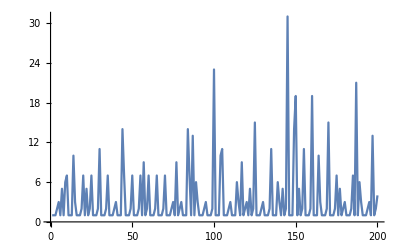

```mathematica
ListLinePlot[%,PlotRange->All]
```

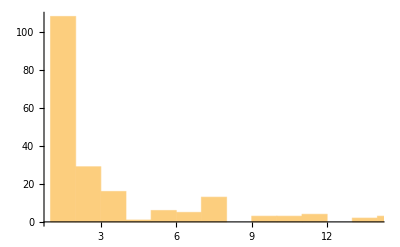

```mathematica
Histogram[%%]
```

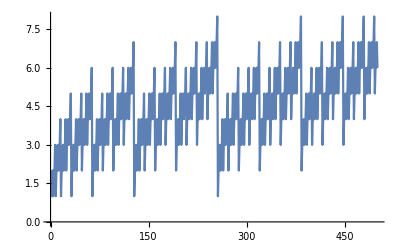

```mathematica
ListLinePlot[Table[DigitCount[n,2,1],{n,500}]]
```

## Other Moduli

```mathematica
Table[ArrayPlot[NestList[Mod[(a+RotateLeft[#])*(b+RotateRight[#]),4]&,CenterArray[{1},100,0],50],PlotLabel->{a,b}],{a,0,3},{b,0,3}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot[NestList[Mod[(1+RotateLeft[#])*(1+RotateRight[#]),4]&,CenterArray[{1,2,1},100,0],50]]
```

-Graphics-

```mathematica
ArrayPlot[NestList[Mod[(1+RotateLeft[#])*(1+RotateRight[#]),4]&,RandomInteger[2,100],50]]
```

-Graphics-

```mathematica
Table[ArrayPlot[NestList[Mod[(a+RotateLeft[#])*(b+RotateRight[#]),4]&,CenterArray[{1,2},100,0],50],PlotLabel->{a,b}],{a,0,3},{b,0,3}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ArrayPlot[NestList[Mod[(a+RotateLeft[#])*(b+RotateRight[#]),5]&,CenterArray[{1,2},100,0],50],PlotLabel->{a,b}],{a,0,4},{b,0,4}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot[Take[NestList[RotateRight[Mod[(3+RotateLeft[#])*(3+RotateRight[#]),5]]&,CenterArray[{1,2},2000,0],2000],1;;-1;;2]]
```

-Graphics-

```mathematica
ArrayPlot[Take[NestList[RotateRight[Mod[(3+RotateLeft[#])*(3+RotateRight[#]),5]]&,CenterArray[{1,2},200,0],200],1;;-1;;2]]
```

-Graphics-

```mathematica
ArrayPlot[Take[NestList[Mod[(3+RotateLeft[#])*(3+RotateRight[#]),5]&,CenterArray[{1,2},200,0],200],1;;-1;;2]]
```

-Graphics-

```mathematica
ArrayPlot[NestList[Mod[(3+RotateLeft[#])*(3+RotateRight[#]),5]&,CenterArray[{1,2},200,0],200]]
```

-Graphics-

```mathematica
ArrayPlot[NestList[Mod[(3+RotateLeft[#])*(3+RotateRight[#]),5]&,CenterArray[{1,2},2000,0],2000]]
```

-Graphics-

```mathematica
ArrayPlot[Take[NestList[Mod[(2+RotateLeft[#])*(4+RotateRight[#]),5]&,CenterArray[{1,2},4000,0],2000],1;;-1;;2]]
```

-Graphics-

```mathematica
N[Exp[Pi Sqrt[163]],100]
```

2.62537412640768743999999999999250072597198185688879353856337336990862707537410378210647910118607313×10^17

```mathematica
FractionalPart[N[Exp[Pi Sqrt[163]],100]]
```

0.999999999999250072597198185688879353856337336990862707537410378210647910118607313